```mathematica
u=(0.7290000000000001-3.1590000000000003 ⅇ^(ⅈ ξ)+5.130000000000001 ⅇ^(2 ⅈ ξ)-3.7 ⅇ^(3 ⅈ ξ)+ⅇ^(4 ⅈ ξ))/(d+(0.2569166666666668-3 d) ⅇ^(ⅈ ξ)+(-0.5413333333333332+3 d) ⅇ^(2 ⅈ ξ)+(0.2854166666666667-d) ⅇ^(3 ⅈ ξ));
```

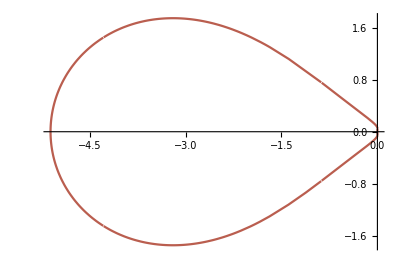

```mathematica
d=-0.2;
p1=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->RGBColor[0.73,0.37,0.31]
,AxesOrigin->{0,0}
,PlotRange->All]
```

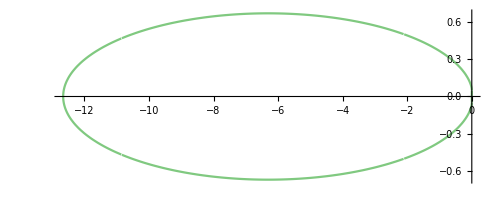

```mathematica
d=0;
p2=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->RGBColor[0.5,0.79,0.5]
,AxesOrigin->{0,0}
,PlotRange->All]
```

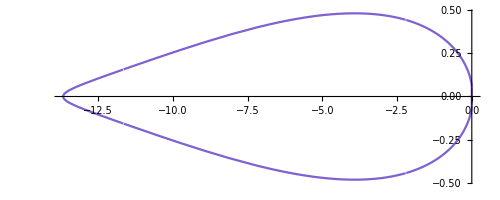

```mathematica
d=0.01;
p3=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->RGBColor[0.5,0.38,0.82]
,AxesOrigin->{0,0}
,PlotRange->All]
```

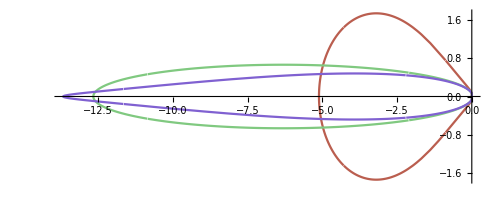

```mathematica
Show[p1,p2,p3]
```

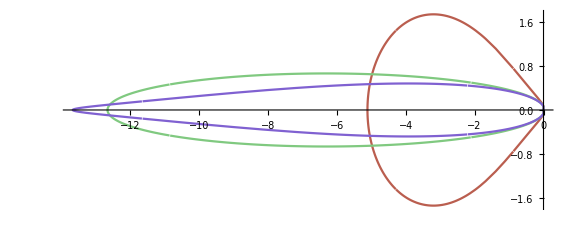

```mathematica
Show[%40,ImageSize->Large]
```

```mathematica
Show[%41,ImageSize->Full]
```

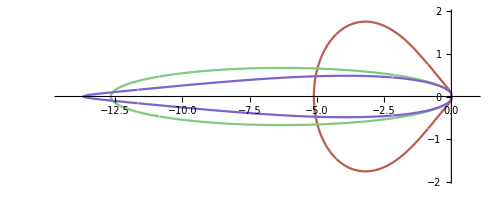

-Graphics-

```mathematica
Show[%,SetOptions[Plot,AspectRatio->0.8],ImageSize->Large]
```

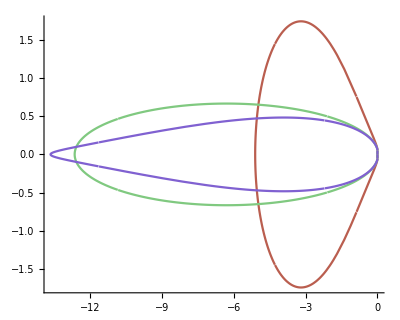

-Graphics-

```mathematica
Show[%1,AxesLabel->{HoldForm[Re Z],HoldForm[Im Z]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

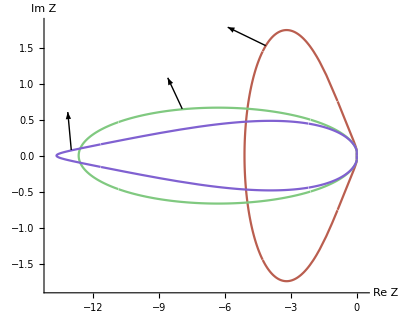

```mathematica
Show[%8,AxesLabel->{HoldForm[Re],HoldForm[Im]},PlotLabel->None,LabelStyle->{GrayLevel[0]},Axes->True,AxesStyle->Arrowheads[0.05]]
```